# Chapter 1

## Example 1.1

```mathematica
Remove["Global`*"]
gr1=Graphics3D[{Arrow[{{0,0,0},{1,1,1}}],Text[Style["A",22],{.9,.9,1}]}];
gr2=Graphics3D[{Arrow[{{0,0,0},{1,0,0}}],Text[Style["i",Red,22],{.9,0.1,0}]}];
gr3=Graphics3D[{Arrow[{{0,0,0},{0,1,0}}],Text[Style["j",Green,22],{0.1,.9,0.05}]}];
gr4=Graphics3D[{Arrow[{{0,0,0},{0,0,1}}],Text[Style["k",Blue,22],{0.05,0.05,.9}]}];Show[{gr1,gr2,gr3,gr4}]
```

Remove::rmnsm: There are no symbols matching "Global`*".

-Graphics3D-

## Example 1.2

```mathematica
Remove["Global`*"]
r={a,b*Sin[a*t],c*t^2};
v=D[r,t];
acc=D[v,t];
Print["Position = ",r]
Print["Velocity = ",v]
Print["Acceleration = ",acc]
```

Position = {a,b Sin[a t],c t^2}

Velocity = {0,a b Cos[a t],2 c t}

Acceleration = {0,-a^2 b Sin[a t],2 c}

## Example 1.3

```mathematica
Remove["Global`*"]
solution=DSolve[{v'[t]==a,v[0]==v0},v,t];
speed=v[t]/.solution[[1]];
Print["The solution of the ODE is v[t] = ",speed]
```

The solution of the ODE is v[t] = a t+v0

## Example 1.4

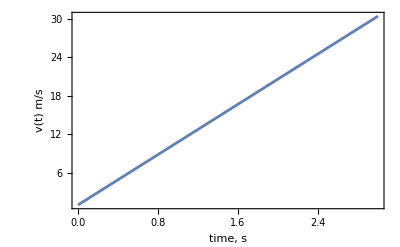

```mathematica
Remove["Global`*"]
SetOptions[Plot,Frame->True,BaseStyle->{FontSize->16},PlotRange->All];
a=9.8;
solution=NDSolve[{v'[t]==a,v[0]==1},v,{t,0,3}];
speed=v[t]/.solution[[1]];
Plot[speed,{t,0,3},FrameLabel->{"time, s","v(t)  m/s"}]
```